```mathematica
p={0,0};
q=1;
```

```mathematica
electricfieldplot[a_,b_,q_]:=Show[StreamPlot[9*10^9 q/((√((x-a)^2+(y-b)^2))^2)*{(x-a)/(√((x-a)^2+(y-b)^2)),(y-b)/(√((x-a)^2+(y-b)^2))},{x,-2,2},{y,-2,2}],Graphics[Disk[{a,b},0.1]]]
```

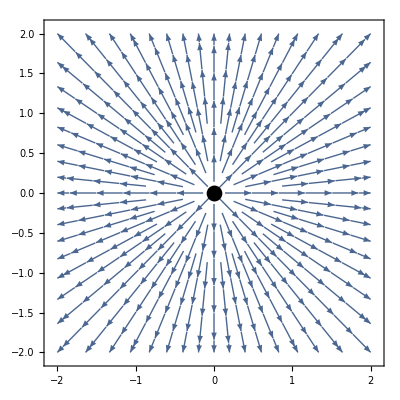

```mathematica
electricfieldplot[0,0,1]
```

```mathematica
electricfieldplot2[a_,b_,q_,c_,d_,r_]:=Show[StreamPlot[9*10^9 q/((√((x-a)^2+(y-b)^2))^2)*{(x-a)/(√((x-a)^2+(y-b)^2)),(y-b)/(√((x-a)^2+(y-b)^2))}+9*10^9 r/((√((x-c)^2+(y-d)^2))^2)*{(x-c)/(√((x-c)^2+(y-d)^2)),(y-d)/(√((x-c)^2+(y-d)^2))},{x,-2,2},{y,-2,2}],Graphics[Disk[{a,b},0.1]],Graphics[Disk[{c,d},0.1]]]
```

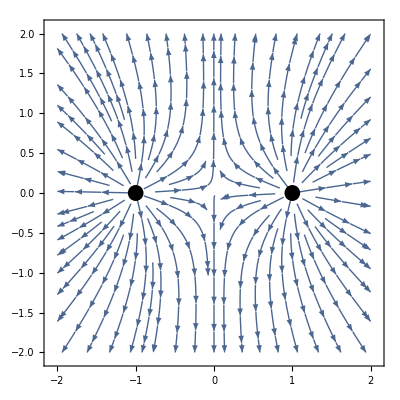

```mathematica
electricfieldplot2[-1,0,1,1,0,1]
```

```mathematica
electricfieldplot3[a_,b_,q_,c_,d_,r_,e_,f_,s_]:=
Show[StreamPlot[9*10^9 q/((√((x-a)^2+(y-b)^2))^2)*{(x-a)/(√((x-a)^2+(y-b)^2)),(y-b)/(√((x-a)^2+(y-b)^2))}+9*10^9 r/((√((x-c)^2+(y-d)^2))^2)*{(x-c)/(√((x-c)^2+(y-d)^2)),(y-d)/(√((x-c)^2+(y-d)^2))}+9*10^9 s/((√((x-e)^2+(y-f)^2))^2)*{(x-e)/(√((x-e)^2+(y-f)^2)),(y-f)/(√((x-e)^2+(y-f)^2))},{x,-2,2},{y,-2,2}],Graphics[Disk[{a,b},0.1]],Graphics[Disk[{c,d},0.1]],Graphics[Disk[{e,f},0.1]]]
```

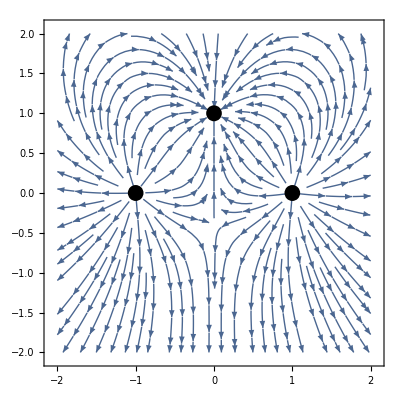

```mathematica
electricfieldplot3[-1,0,1,1,0,1,0,1,-1]
```

```mathematica
Export["electric3.gif",ListAnimate[Table[electricfieldplot3[-1,0,1,1,0,1,n^2-2,n,-1],{n,-2,2,0.2}]]]
```

electric3.gif

```mathematica
Export["electric2.gif",ListAnimate[Table[electricfieldplot2[-1,0,1,1,0,n],{n,-10,10}]]]
```